```mathematica
G==6.67*10^(-11)
c==3*10^8
```

G==6.67×10^-11

c==300000000

```mathematica
G==6.67*10^(-11)
c==3*10^8
ρ==3*10^3
R==6*10^6
```

G==6.67×10^-11

c==300000000

ρ==3000

R==6000000

```mathematica
k[r_]:=((3300000000^2-8Pi 6.67*^-11 3000 r^2)/(3300000000^2-8Pi 6.67*^-11 3000 6000000^2))^(1/2)
```

```mathematica
P[r_]:=(1-k[r])/(3k[r]-1)3000 300000000^2
P[6000000]
```

0.

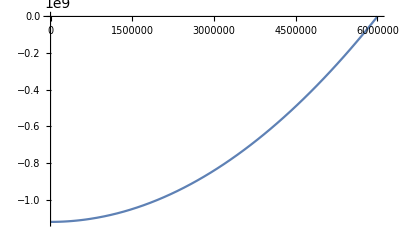

```mathematica
Plot[P[r],{r,0,6000000}]
```

```mathematica
k[r_]:=((3300000000^2-8Pi 6.67*^-11 3000 6000000^2)/(3300000000^2-8Pi 6.67*^-11 3000 r^2))^(1/2)
P[r_]:=(1-k[r])/(3k[r]-1)3000 300000000^2
```

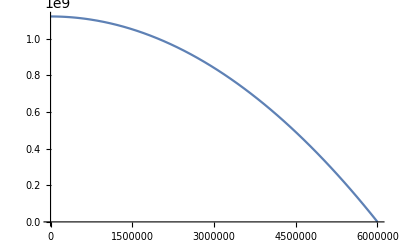

```mathematica
Plot[P[r],{r,0,6000000}]
```